```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/charlie/research/collins2018/mathematica

```mathematica
<<ErrorBarLogPlots`
```

```mathematica
avk = 0.57
avp=0.12
```

0.57

0.12

## Read and interpolate DSS collinear fragmentation functions.

```mathematica
DSShplus= ReadList["fragmentationpiplus.dat",Real,RecordLists-> True];
DSShminus= ReadList["fragmentationpiminus.dat",Real,RecordLists-> True];
```

```mathematica
uhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,3]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}]
dhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,4]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
shplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,5]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
ubhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,6]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
dbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,7]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
sbhplus=Interpolation[Table[{{DSShplus[[i,1]],DSShplus[[i,2]]},DSShplus[[i,8]]},{i,1,Length[DSShplus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.010098, 0.989902}, {1., 89.11}}, <>]

```mathematica
uhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,3]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}]
dhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,4]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
shminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,5]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
ubhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,6]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
dbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,7]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
sbhminus=Interpolation[Table[{{DSShminus[[i,1]],DSShminus[[i,2]]},DSShminus[[i,8]]},{i,1,Length[DSShminus]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction[{{0.010098, 0.989902}, {1., 89.11}}, <>]

InterpolatingFunction::dmval: Input value {0.0100202,3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

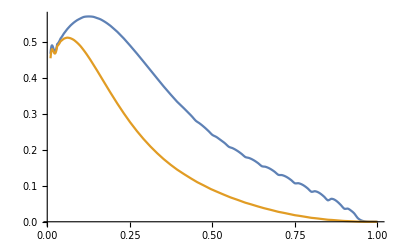

```mathematica
Plot[{z uhplus[z,3.],z dhplus[z,3.]},{z,0.01,1}]
```

## D_1

```mathematica
(*2005 fit Appendix A.1 [hep-ph/0501196]*)
Clear[avp];
avp=0.2;
(* fragmentation*)
D1uTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1ubarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1dbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]
D1sbarTMD[pion_,z_,Q2_, pt_]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]] 1/(π avp) Exp[-pt^2/avp]


D1u[pion_,z_,Q2_ ]:= If[pion == "pi+",uhplus[z,Q2],If[pion == "pi-",uhminus[z,Q2]]]  
D1d[pion_,z_,Q2_ ]:= If[pion == "pi+",dhplus[z,Q2],If[pion == "pi-",dhminus[z,Q2]]]  
D1ubar[pion_,z_,Q2_ ]:= If[pion == "pi+",ubhplus[z,Q2],If[pion == "pi-",ubhminus[z,Q2]]]  
D1dbar[pion_,z_,Q2_ ]:= If[pion == "pi+",dbhplus[z,Q2],If[pion == "pi-",dbhminus[z,Q2]]]  
D1s[pion_,z_,Q2_ ]:= If[pion == "pi+",shplus[z,Q2],If[pion == "pi-",shminus[z,Q2]]]  
D1sbar[pion_,z_,Q2_ ]:= If[pion == "pi+",sbhplus[z,Q2],If[pion == "pi-",sbhminus[z,Q2]]]
```

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

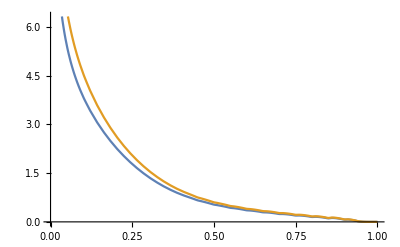

```mathematica
Plot[{D1u["pi+",z,1.],D1d["pi-",z,1.]},{z,0,1}]
```

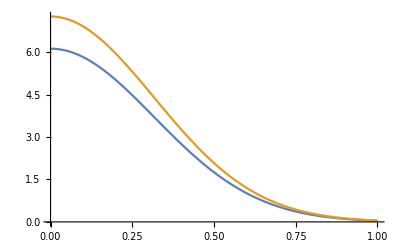

```mathematica
Plot[{D1uTMD["pi+",0.1,1.,pt],D1dTMD["pi-",0.1,1.,pt]},{pt,0,1}]
```

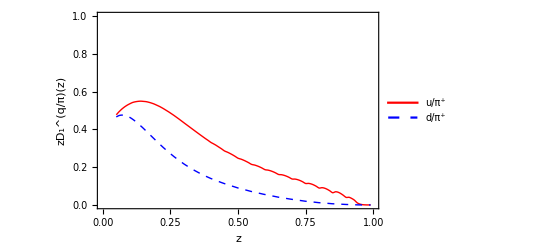

```mathematica
D1plot =Plot[{x D1u["pi+",x,2.4],x D1d["pi+",x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zD_1^(q/π)(z)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.7}]]
```

## Read and interpolate Soffer Bound collinear distribution functions.

```mathematica
sb= ReadList["SofferBound.dat",Real,RecordLists-> True];
```

```mathematica
sb1u=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,3]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1d=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,4]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1s=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,5]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1ubar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,6]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1dbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,7]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
sb1sbar=Interpolation[Table[{{sb[[i,1]],sb[[i,2]]},sb[[i,8]]},{i,1,Length[sb]}],InterpolationOrder->{3,3}];
```

InterpolatingFunction::dmval: Input value {0.0100202,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

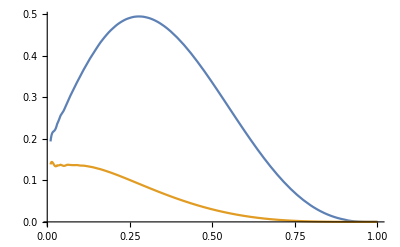

```mathematica
Plot[{x*sb1u[x,1.],x*sb1d[x,1.]},{x,0.01,1}]
```

## h_1

```mathematica
Clear[NuT,NdT,alphaT,betaT];
NuT=0.37;
NdT=-1.000;
alphaT=0.75;
betaT=2.35;

(* Transversity function with DGLAP Evolution*)
h1u[x_,Q2_]:=(NuT x^alphaT (1-x)^betaT(alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT))) sb1u[x,Q2];
h1d[x_,Q2_]:=(NdT x^alphaT (1-x)^betaT (alphaT+ betaT)^(alphaT+ betaT)/((alphaT^alphaT)( betaT^betaT)))sb1d[x,Q2];

h1uTMD[x_,Q2_,kt_]:=h1u[x,Q2]1/(π avk) Exp[-kt^2/avk];
h1dTMD[x_,Q2_,kt_]:=h1d[x,Q2]1/(π avk) Exp[-kt^2/avk];


year = 2018;
width = 57;
MyLabel= StringForm["`` fit ⟨k_⊥^2⟩ = 0.`` (GeV^2).",year,width]
```

2018 fit ⟨k_⊥^2⟩ = 0.57 (GeV^2).

InterpolatingFunction::dmval: Input value {0.0010202,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

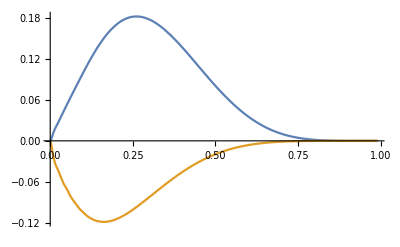

```mathematica
Plot[{x h1u[x,1.], x h1d[x,1.]},{x,0.001,0.99}]
```

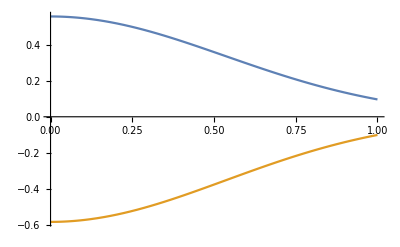

```mathematica
Plot[{h1uTMD[0.1,1.,kt],h1dTMD[0.1,1.,kt]},{kt,0,1}]
```

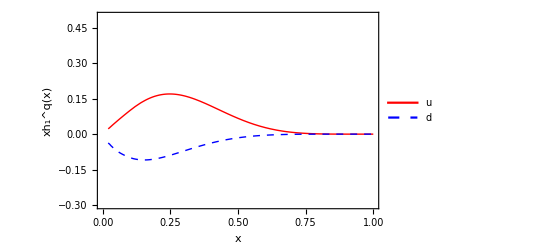

```mathematica
h1plot =Plot[{x h1u[x,2.4],x h1d[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.3,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xh_1^q(x)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

## H_1^⊥

```mathematica
Clear[MC,NCfav,NCunf,alphaC,betaC, Mh];
MC=Sqrt[0.30];
NCfav=0.52;
NCunf=-0.43;
alphaC=0.73;
betaC=0.0000001;
Mh = 0.139;

(*Collins function with DGLAP Evolution*)
H1perpFavHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));
H1perpUnfHalfMoment[x_,Q2_]:=√(2 ⅇ)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2]/4 √((π avp)/((MC^2+avp)^3));

H1perpFavFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC))) D1u["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);
H1perpUnfFirstMoment[x_,Q2_]:=√(ⅇ/2)(NCunf x^alphaC(1-x)^betaC (alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1d["pi+",x,Q2] (MC^3 avp)/(Mh x(MC^2+avp)^2);

H1perpFavTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCfav x^alphaC(1-x)^betaC(alphaC+ betaC)^(alphaC+ betaC)/((alphaC^alphaC)( betaC^betaC)))D1u["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];
H1perpUnfTMD[x_,Q2_,kt_]:=(x Mh)/MC Exp[-kt^2/MC^2] √(2 ⅇ)(NCunf )D1d["pi+",x,Q2]1/(π avp) Exp[-kt^2/avp];


year = 2018;
width = 12;
MyLabel= StringForm["`` fit ⟨p_⊥^2⟩ = 0.`` (GeV^2).",year,width]

H1perpFirstMoment[quark_,pion_,x_,Q2_] := If[(quark == "u" && pion == "pi+") || (quark == "bard" && pion == "pi+") || (quark == "d" && pion == "pi-") || (quark == "baru" && pion == "pi-"),H1perpFavFirstMoment[x,Q2],H1perpUnfFirstMoment[x,Q2]]
```

2018 fit ⟨p_⊥^2⟩ = 0.12 (GeV^2).

```mathematica
H1perpFavFirstMoment[.1,2.4]
```

5.72047

InterpolatingFunction::dmval: Input value {0.0000204286,1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

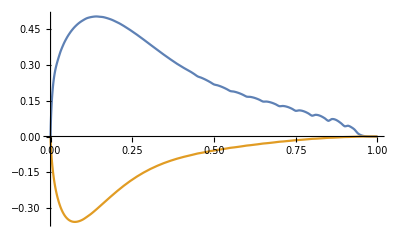

```mathematica
Plot[{H1perpFavHalfMoment[z,1.],H1perpUnfHalfMoment[z,1.]},{z,0,1}]
```

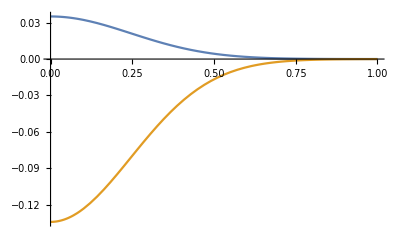

```mathematica
Plot[{H1perpFavTMD[0.1,1.,pt],H1perpUnfTMD[0.1,1.,pt]},{pt,0,1}]
```

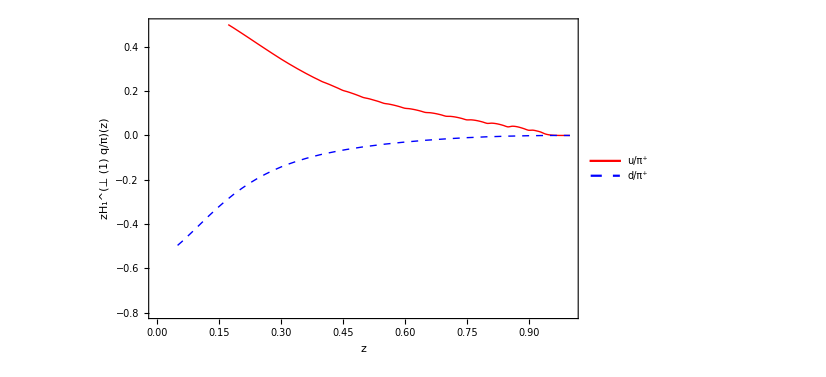

```mathematica
H1perpplot =Plot[{x H1perpFavFirstMoment[x,2.4],x H1perpUnfFirstMoment[x,2.4]},{x,0.05,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.8,0.5}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"z","zH_1^(⊥ (1) q/π)(z)"},BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u/π^+","d/π^+"},{0.7,0.3}]]
```

```mathematica
dataH1perpFavFirstMomentTable = Table[{z,H1perpFavFirstMoment[z,2.4]},{z,0.02,0.98,0.01}]
dataH1perpUnfFirstMomentTable = Table[{z, H1perpUnfFirstMoment[z,2.4]},{z,0.02,0.98,0.01}]
```

(0.02 | 34.1504
0.03 | 21.5478
0.04 | 15.685
0.05 | 12.2922
0.06 | 10.0797
0.07 | 8.518
0.08 | 7.3513
0.09 | 6.44582
0.1 | 5.72047
0.11 | 5.13128
0.12 | 4.62592
0.13 | 4.19646
0.14 | 3.82684
0.15 | 3.49868
0.16 | 3.21511
0.17 | 2.95916
0.18 | 2.73058
0.19 | 2.52521
0.2 | 2.33705
0.21 | 2.16923
0.22 | 2.01413
0.23 | 1.8727
0.24 | 1.74324
0.25 | 1.62264
0.26 | 1.51394
0.27 | 1.41207
0.28 | 1.31849
0.29 | 1.23223
0.3 | 1.15092
0.31 | 1.07785
0.32 | 1.00855
0.33 | 0.94475
0.34 | 0.885773
0.35 | 0.82956
0.36 | 0.779566
0.37 | 0.731561
0.38 | 0.687426
0.39 | 0.646634
0.4 | 0.607237
0.41 | 0.575045
0.42 | 0.543266
0.43 | 0.512057
0.44 | 0.481564
0.45 | 0.451907
0.46 | 0.430266
0.47 | 0.408246
0.48 | 0.386078
0.49 | 0.363964
0.5 | 0.342077
0.51 | 0.327633
0.52 | 0.31224
0.53 | 0.296191
0.54 | 0.27974
0.55 | 0.26311
0.56 | 0.25349
0.57 | 0.242512
0.58 | 0.230519
0.59 | 0.217808
0.6 | 0.204656
0.61 | 0.198303
0.62 | 0.190261
0.63 | 0.18093
0.64 | 0.170661
0.65 | 0.159782
0.66 | 0.15568
0.67 | 0.149584
0.68 | 0.141972
0.69 | 0.133259
0.7 | 0.123841
0.71 | 0.121377
0.72 | 0.116587
0.73 | 0.110061
0.74 | 0.102311
0.75 | 0.0938221
0.76 | 0.0927677
0.77 | 0.0889283
0.78 | 0.0830867
0.79 | 0.0759108
0.8 | 0.0680209
0.81 | 0.0684944
0.82 | 0.0654128
0.83 | 0.0599373
0.84 | 0.0530218
0.85 | 0.0455191
0.86 | 0.0483861
0.87 | 0.045995
0.88 | 0.0404573
0.89 | 0.0333998
0.9 | 0.0260777
0.91 | 0.0262631
0.92 | 0.0219743
0.93 | 0.0160342
0.94 | 0.00732815
0.95 | 0.00290558
0.96 | 0.00093937
0.97 | 0.000219853
0.98 | 0.0000288273)

(0.02 | -27.7861
0.03 | -17.6509
0.04 | -12.805
0.05 | -9.91887
0.06 | -7.99555
0.07 | -6.60701
0.08 | -5.5625
0.09 | -4.74489
0.1 | -4.09202
0.11 | -3.55249
0.12 | -3.10703
0.13 | -2.73209
0.14 | -2.4131
0.15 | -2.14081
0.16 | -1.90497
0.17 | -1.70068
0.18 | -1.52273
0.19 | -1.36687
0.2 | -1.22958
0.21 | -1.10914
0.22 | -1.00209
0.23 | -0.907363
0.24 | -0.823206
0.25 | -0.747613
0.26 | -0.68108
0.27 | -0.620895
0.28 | -0.56709
0.29 | -0.518833
0.3 | -0.474827
0.31 | -0.436066
0.32 | -0.400487
0.33 | -0.368435
0.34 | -0.339469
0.35 | -0.312693
0.36 | -0.289073
0.37 | -0.267094
0.38 | -0.247164
0.39 | -0.229028
0.4 | -0.212041
0.41 | -0.197503
0.42 | -0.183729
0.43 | -0.170693
0.44 | -0.158371
0.45 | -0.14674
0.46 | -0.137153
0.47 | -0.127938
0.48 | -0.119106
0.49 | -0.110663
0.5 | -0.102613
0.51 | -0.0960564
0.52 | -0.0896671
0.53 | -0.0834712
0.54 | -0.0774899
0.55 | -0.0717405
0.56 | -0.0671433
0.57 | -0.0626023
0.58 | -0.0581507
0.59 | -0.0538165
0.6 | -0.0496243
0.61 | -0.046322
0.62 | -0.0430221
0.63 | -0.0397602
0.64 | -0.0365665
0.65 | -0.0334687
0.66 | -0.0311164
0.67 | -0.0287316
0.68 | -0.0263523
0.69 | -0.0240106
0.7 | -0.021736
0.71 | -0.0200823
0.72 | -0.0183761
0.73 | -0.0166575
0.74 | -0.0149603
0.75 | -0.0133151
0.76 | -0.0121957
0.77 | -0.01101
0.78 | -0.0098014
0.79 | -0.00860609
0.8 | -0.00745549
0.81 | -0.00675714
0.82 | -0.00597807
0.83 | -0.00516857
0.84 | -0.00436864
0.85 | -0.00361134
0.86 | -0.00324347
0.87 | -0.00277531
0.88 | -0.00227138
0.89 | -0.00177934
0.9 | -0.00133302
0.91 | -0.00110174
0.92 | -0.000826178
0.93 | -0.000562371
0.94 | -0.000256967
0.95 | -0.000101887
0.96 | -0.0000329398
0.97 | -7.70933×10^-6
0.98 | -1.01086×10^-6)

```mathematica
datah1uTable = Table[{x,h1u[x,2.4]},{x,0.02,0.98,0.01}]
datah1dTable = Table[{x,h1d[x,2.4]},{x,0.02,0.98,0.01}]
```

(0.02 | 1.12365
0.03 | 1.07541
0.04 | 1.06267
0.05 | 1.03316
0.06 | 1.03639
0.07 | 1.02481
0.08 | 1.01512
0.09 | 1.0091
0.1 | 0.995963
0.11 | 0.988139
0.12 | 0.975051
0.13 | 0.960511
0.14 | 0.944907
0.15 | 0.925921
0.16 | 0.90723
0.17 | 0.885929
0.18 | 0.863388
0.19 | 0.839847
0.2 | 0.814697
0.21 | 0.789315
0.22 | 0.762807
0.23 | 0.735768
0.24 | 0.708367
0.25 | 0.68047
0.26 | 0.652652
0.27 | 0.624652
0.28 | 0.596746
0.29 | 0.569048
0.3 | 0.541558
0.31 | 0.514517
0.32 | 0.487878
0.33 | 0.461763
0.34 | 0.436242
0.35 | 0.411343
0.36 | 0.387152
0.37 | 0.363685
0.38 | 0.34098
0.39 | 0.319072
0.4 | 0.297987
0.41 | 0.277716
0.42 | 0.258305
0.43 | 0.239761
0.44 | 0.222087
0.45 | 0.205282
0.46 | 0.189284
0.47 | 0.174149
0.48 | 0.159863
0.49 | 0.14641
0.5 | 0.133769
0.51 | 0.121865
0.52 | 0.11074
0.53 | 0.100369
0.54 | 0.0907259
0.55 | 0.0817806
0.56 | 0.0734573
0.57 | 0.0657839
0.58 | 0.0587289
0.59 | 0.0522605
0.6 | 0.0463472
0.61 | 0.0409236
0.62 | 0.0360012
0.63 | 0.0315482
0.64 | 0.0275335
0.65 | 0.0239267
0.66 | 0.0206765
0.67 | 0.0177827
0.68 | 0.0152168
0.69 | 0.0129515
0.7 | 0.0109608
0.71 | 0.00920683
0.72 | 0.0076836
0.73 | 0.00636806
0.74 | 0.0052386
0.75 | 0.00427499
0.76 | 0.00345201
0.77 | 0.00276141
0.78 | 0.00218653
0.79 | 0.00171214
0.8 | 0.00132436
0.81 | 0.00100788
0.82 | 0.000755663
0.83 | 0.000557225
0.84 | 0.000403318
0.85 | 0.000285843
0.86 | 0.000196849
0.87 | 0.000131885
0.88 | 0.0000855893
0.89 | 0.0000535094
0.9 | 0.0000319797
0.91 | 0.0000164336
0.92 | 7.8007×10^-6
0.93 | 3.35033×10^-6
0.94 | 1.26229×10^-6
0.95 | 3.9767×10^-7
0.96 | 9.6667×10^-8
0.97 | 1.55949×10^-8
0.98 | 1.19284×10^-9)

(0.02 | -1.87472
0.03 | -1.6296
0.04 | -1.4959
0.05 | -1.3513
0.06 | -1.28051
0.07 | -1.19483
0.08 | -1.11953
0.09 | -1.05689
0.1 | -0.990648
0.11 | -0.936248
0.12 | -0.880474
0.13 | -0.827505
0.14 | -0.777645
0.15 | -0.728285
0.16 | -0.683024
0.17 | -0.638747
0.18 | -0.596679
0.19 | -0.556854
0.2 | -0.518461
0.21 | -0.482764
0.22 | -0.448558
0.23 | -0.416302
0.24 | -0.385949
0.25 | -0.357104
0.26 | -0.330292
0.27 | -0.304913
0.28 | -0.28114
0.29 | -0.258908
0.3 | -0.237992
0.31 | -0.218603
0.32 | -0.200423
0.33 | -0.183498
0.34 | -0.167765
0.35 | -0.153092
0.36 | -0.139543
0.37 | -0.126948
0.38 | -0.115299
0.39 | -0.104543
0.4 | -0.0945977
0.41 | -0.0854812
0.42 | -0.0770797
0.43 | -0.0693531
0.44 | -0.0622622
0.45 | -0.0557688
0.46 | -0.0498653
0.47 | -0.0444793
0.48 | -0.0395764
0.49 | -0.0351237
0.5 | -0.0310894
0.51 | -0.0274506
0.52 | -0.0241691
0.53 | -0.0212173
0.54 | -0.0185691
0.55 | -0.0162
0.56 | -0.0140873
0.57 | -0.012208
0.58 | -0.0105415
0.59 | -0.00906837
0.6 | -0.00777055
0.61 | -0.00663034
0.62 | -0.00563309
0.63 | -0.00476418
0.64 | -0.00401012
0.65 | -0.00335848
0.66 | -0.00279719
0.67 | -0.00231665
0.68 | -0.00190728
0.69 | -0.00156036
0.7 | -0.00126798
0.71 | -0.00102273
0.72 | -0.000818615
0.73 | -0.000649878
0.74 | -0.00051139
0.75 | -0.000398607
0.76 | -0.000307407
0.77 | -0.000234447
0.78 | -0.000176651
0.79 | -0.000131353
0.8 | -0.0000962629
0.81 | -0.0000693917
0.82 | -0.0000491431
0.83 | -0.0000341233
0.84 | -0.000023176
0.85 | -0.0000153528
0.86 | -9.87429×10^-6
0.87 | -6.14708×10^-6
0.88 | -3.68485×10^-6
0.89 | -2.11315×10^-6
0.9 | -1.14893×10^-6
0.91 | -5.3135×10^-7
0.92 | -2.24195×10^-7
0.93 | -8.42526×10^-8
0.94 | -2.72081×10^-8
0.95 | -7.14259×10^-9
0.96 | -1.38879×10^-9
0.97 | -1.67947×10^-10
0.98 | -8.62381×10^-12)

```mathematica
H1perpFavFirstMomentGuess[z_]=Nfav * z^c*(1.-z)^d
```

Nfav z^c (1.-z)^d

```mathematica
H1perpUnfFirstMomentGuess[z_]=Nunf * z^c*(1.-z)^d
```

Nunf z^c (1.-z)^d

```mathematica
h1uGuess[x_]=Nu * x^au*(1.-x)^bu
h1dGuess[x_]=-Nd * x^ad*(1.-x)^bd
```

Nu x^au (1.-x)^bu

-Nd x^ad (1.-x)^bd

```mathematica
h1uGuessFit=NonlinearModelFit[datah1uTable,{h1uGuess[x]},{Nu,au,bu},{x}]
```

FittedModel[2.71035 (1.-x)^3.8386 x^0.239414]

```mathematica
h1dGuessFit=NonlinearModelFit[datah1dTable,{h1dGuess[x]},{Nd,ad,bd},{x}]
```

FittedModel[-(1.32577 (1.-x)^5.10632)/x^0.106715]

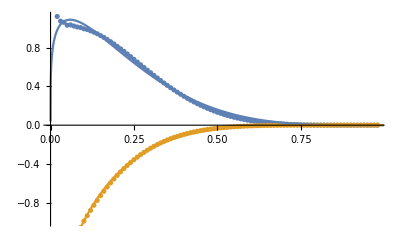

```mathematica
Show[ListPlot[{datah1uTable,datah1dTable}],Plot[{h1uGuessFit [x],h1dGuessFit[x]},{x,0,1}]]
```

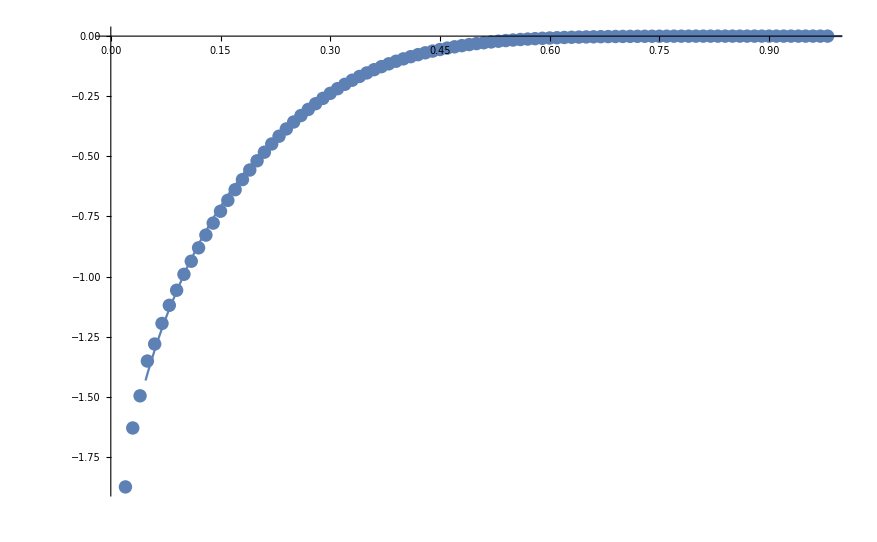

```mathematica
Show[ListPlot[{datah1dTable}],Plot[{h1dGuessFit[x]},{x,0,1}]]
```

```mathematica
allH1perpFirstMomentGuessData=Join[{1,Sequence@@#}&/@dataH1perpFavFirstMomentTable,{2,Sequence@@#}&/@dataH1perpUnfFirstMomentTable];
```

```mathematica
H1perpFirstMomentGuess[index_,z_]:=KroneckerDelta[index-1] H1perpFavFirstMomentGuess[z]+KroneckerDelta[index-2] H1perpUnfFirstMomentGuess[z]
```

```mathematica
H1perpFirstMomentGuessFit = NonlinearModelFit[allH1perpFirstMomentGuessData,H1perpFirstMomentGuess[index,z],{Nfav,Nunf,c,d},{index,z}]
```

FittedModel[(0.636296 (1.-z)^2.24624 1-index)/z^1.03066-(0.50632 (1.-z)^2.24624 2-index)/z^1.03066]

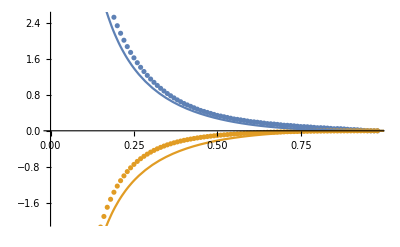

```mathematica
Show[ListPlot[{dataH1perpFavFirstMomentTable,dataH1perpUnfFirstMomentTable}],Plot[{H1perpFirstMomentGuessFit [1,z],H1perpFirstMomentGuessFit [2,z]},{z,0,1}]]
```